```mathematica
ClearAll["Global`*"]
```

```mathematica
lo[n_, k_ ]:= Sum[ (-1)^(j+1) lo[ Floor[n/j],k-1],{j,1,n}];lo[n_, 1] := Sum[ (-1)^(j+1) Log[j],{j,1,n}]
t[n_, a_] := Mod[n,a]-Mod[n-1,a]
lp[n_, k_,b_ ]:= Sum[ t[j,b] lp[ Floor[n/j],k-1,b],{j,1,n}];lp[n_, 1,b_] := Sum[ t[j,b] Log[j],{j,1,n}]
fa[n_,k_] := Sum[ 2^j Binomial[k,j] (-1)^j l1[n/2^j,k],{j,0,k}]+Sum[ 2^j Binomial[k-1,j-1](-1)^j Log[2] d1[n/2^j,k],{j,1,k}]

L1[n_, k_ ]:= Sum[ L1[Floor[n/j],k-1],{j,1,n}];L1[n_, 1] := Sum[ Log[j],{j,1,n}];L1[n_,0]:=1
L2[n_, k_ ]:= Sum[ L2[Floor[n/j],k-1],{j,2,n}];L2[n_, 1] := Sum[ Log[j],{j,2,n}]
D1[n_, k_] := Sum[ D1[Floor[n/j],k-1],{j,1,n}];D1[n_, 0] := 1
L2toL1[n_,z_]:=Sum[FactorialPower[z-1,a]/a! L2[n,a+1],{a,0,Log[2,n]}]
L2toL1x[n_,z_]:=Sum[Binomial[z-1,a] L2[n,a+1],{a,0,Log[2,n]}]
L1toL2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k-1,j-1] L1[n,j],{j,1,k}]

EL[n_, k_,b_ ]:= EL[n,k,b]=Sum[ EL[ n/j,k-1,b],{j,1,n}]-b Sum[ EL[ n/(j b),k-1,b],{j,1,n}];EL[n_, 1,b_] := EL[n,1,b]=Sum[ Log[j],{j,1,n}]-b Sum[ Log[j b],{j,1,n/b}]
LtoEL[n_,k_,b_] := Sum[ b^j Binomial[k,j] (-1)^j L1[n/b^j,k],{j,0,k}]+Sum[ b^j Binomial[k-1,j-1](-1)^j Log[b] D1[n/b^j,k],{j,1,k}]

EL1toL1[n_, b_] := Sum[ b^j EL[n/b^j,1,b],{j,0,Log[b,n]}] + Log[b]Sum[ b^j D1[n/b^j,1],{j,1,Log[b,n]}]

EL2[n_, k_,b_ ]:= EL2[n,k,b]=Sum[ EL2[ n/j,k-1,b],{j,2,n}]-b Sum[ EL2[ n/(j b),k-1,b],{j,1,n}];EL2[n_, 1,b_] := EL2[n,1,b]=Sum[ Log[j],{j,2,n}]-b Sum[ Log[j b],{j,1,n/b}]
EL2toEL1[n_,z_,b_]:=Sum[FactorialPower[z-1,a]/a! EL2[n,a+1,b],{a,0,Log[If[ b<2,b,2],n]}]
EL1toEL2[n_,k_,b_]:=Sum[(-1)^(k-j) Binomial[k-1,j-1] EL[n,j,b],{j,1,k}]
```

```mathematica
N[L2toL1x[100,0]]
```

94.0453

```mathematica
N[EL2toEL1[100,0,101]]
```

94.0453

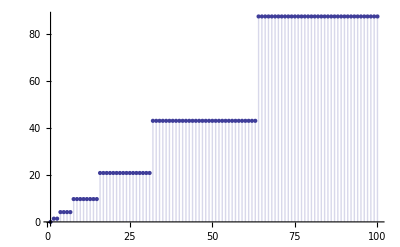

```mathematica
DiscretePlot[L2toL1[n,0]-EL2toEL1[n,0,2],{n,1,100}]
```

```mathematica
N[EL1toEL2[160,3,2.5]]
```

-138.321

```mathematica
N[LtoEL[100,2,4.3]]
```

24.3806

```mathematica
N[EL[100,2,4.3]]
```

24.3806

```mathematica
{N[L2toL1[100,2]],N[L1[100,2]],N[L2[100,2]+L2[100,1]]}
```

{920.841,920.841,920.841}

```mathematica
{N[L2toL1[100,3]],N[L1[100,3]],N[L2[100,3]+2L2[100,2]+L2[100,1]]}
```

{1921.09,1921.09,1921.09}

```mathematica
{N[L2toL1[100,4]],N[L1[100,4]],N[L2[100,4]+3L2[100,3]+3L2[100,2]+L2[100,1]]}
```

{3559.46,3559.46,3559.46}

```mathematica
N[L2toL1[100,0]]
```

94.0453

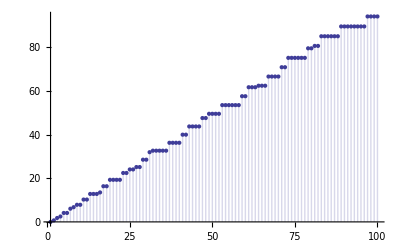

```mathematica
DiscretePlot[ L2toL1[n,0],{n,1,100}]
```

```mathematica
f1[n_] := Sum[ (-1)^(j+k)Log[k],{j,1,n},{k,1,n/j}]
```

```mathematica
N[f1[100]]
```

3.9172

```mathematica
f2[n_] := Sum[ (-1)^(k+1)Log[k],{j,1,n},{k,1,n/j}]-2Sum[ (-1)^(k+1)Log[k],{j,2,n,2},{k,1,n/j}]
```

```mathematica
N[f2[100]]
```

3.9172

```mathematica
f3[n_] := Sum[ Log[k],{j,1,n},{k,1,n/j}]-2Sum[Log[k],{j,1,n},{k,2,n/j,2}]-2Sum[ Log[k],{j,2,n,2},{k,1,n/j}]+4Sum[ Log[k],{j,2,n,2},{k,2,n/j,2}]
```

```mathematica
N[f3[100]]
```

3.9172

```mathematica
f4[n_] := Sum[ Log[k],{j,1,n},{k,1,n/j}]-2Sum[Log[2k],{j,1,n},{k,1,n/(2j)}]-2Sum[ Log[k],{j,1,n/2},{k,1,n/(2j)}]+4Sum[ Log[2 k],{j,1,n/2},{k,1,n/(4j)}]
```

```mathematica
N[f4[100]]
```

3.9172

```mathematica
f5[n_] := Sum[ Log[k],{j,1,n},{k,1,n/j}]-2Sum[Log[2]+Log[k],{j,1,n},{k,1,n/(2j)}]-2Sum[ Log[k],{j,1,n/2},{k,1,n/(2j)}]+4Sum[ Log[2]+Log[k],{j,1,n/2},{k,1,n/(4j)}]
```

```mathematica
N[f5[100]]
```

3.9172

```mathematica
f6[n_] := Sum[ Log[k],{j,1,n},{k,1,n/j}]-2Sum[Log[k],{j,1,n},{k,1,n/(2j)}]-2Sum[ Log[k],{j,1,n/2},{k,1,n/(2j)}]+
4Sum[ Log[k],{j,1,n/2},{k,1,n/(4j)}]-
Log[2]2Sum[1,{j,1,n},{k,1,n/(2j)}]+
Log[2]4Sum[ 1,{j,1,n/2},{k,1,n/(4j)}]
```

```mathematica
N[f6[100]]
```

3.9172

```mathematica
f7[n_] := Sum[ Log[k],{j,1,n},{k,1,n/j}]-4Sum[Log[k],{j,1,n/2},{k,1,n/(2j)}]+
4Sum[ Log[k],{j,1,n/4},{k,1,n/(4j)}]-
2Log[2]Sum[1,{j,1,n/2},{k,1,n/(2j)}]+
4Log[2]Sum[ 1,{j,1,n/4},{k,1,n/(4j)}]
```

```mathematica
N[f7[100]]
```

3.9172

```mathematica
g1[n_] := Sum[ (-1)^(j+k+m+1)Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]
```

```mathematica
N[g1[100]]
```

4.38425

```mathematica
g2[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]-2Sum[ Log[m],{j,2,n,2},{k,1,n/j},{m,1,n/(j k)}]-2Sum[ Log[m],{j,1,n},{k,2,n/j,2},{m,1,n/(j k)}]-2Sum[ Log[m],{j,1,n},{k,1,n/j},{m,2,n/(j k),2}]+4Sum[ Log[m],{j,2,n,2},{k,2,n/j,2},{m,1,n/(j k)}]+4Sum[ Log[m],{j,2,n,2},{k,1,n/j},{m,2,n/(j k),2}]+4Sum[ Log[m],{j,1,n},{k,2,n/j,2},{m,2,n/(j k),2}]-8Sum[ Log[m],{j,2,n,2},{k,2,n/j,2},{m,2,n/(j k),2}]
```

```mathematica
N[g2[100]]
```

4.38425

```mathematica
g3[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]-2Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(2j k)}]-2Sum[ Log[m],{j,1,n},{k,1,n/(2j)},{m,1,n/(2j k)}]-2Sum[ Log[2 m],{j,1,n},{k,1,n/j},{m,1,n/(2j k)}]+4Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Sum[ Log[2m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Sum[ Log[2m],{j,1,n},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[2m],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]
```

```mathematica
N[g3[100]]
```

4.38425

```mathematica
g4[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]-2Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(2j k)}]-2Sum[ Log[m],{j,1,n},{k,1,n/(2j)},{m,1,n/(2j k)}]-2Sum[ Log[ m],{j,1,n},{k,1,n/j},{m,1,n/(2j k)}]+4Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Sum[ Log[m],{j,1,n},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[m],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]-2Sum[ Log[2],{j,1,n},{k,1,n/j},{m,1,n/(2j k)}]+4Sum[ Log[2],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Sum[ Log[2],{j,1,n},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[2],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]
```

```mathematica
N[g4[100]]
```

4.38425

```mathematica
g5[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]-6Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(2j k)}]+12Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[m],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]-2Sum[ Log[2],{j,1,n},{k,1,n/j},{m,1,n/(2j k)}]+4Sum[ Log[2],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Sum[ Log[2],{j,1,n},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[2],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]
```

```mathematica
N[g5[100]]
```

4.38425

```mathematica
g6[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]-6Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(2j k)}]+12Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[m],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]-2Log[2]Sum[ 1,{j,1,n},{k,1,n/j},{m,1,n/(2j k)}]+4Log[2]Sum[ 1,{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]+4Log[2]Sum[ 1,{j,1,n},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Log[2]Sum[1,{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]
```

```mathematica
N[g6[100]]
```

4.38425

```mathematica
g7[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{m,1,n/(j k)}]-6Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(2j k)}]+12Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{m,1,n/(4j k)}]-8Sum[ Log[m],{j,1,n/2},{k,1,n/(4j)},{m,1,n/(8j k)}]-2Log[2]Sum[ 1,{j,1,n/2},{k,1,n/(2j)},{m,1,n/(2j k)}]+8Log[2]Sum[ 1,{j,1,n/4},{k,1,n/(4j)},{m,1,n/(4j k)}]-8Log[2]Sum[1,{j,1,n/8},{k,1,n/(8j)},{m,1,n/(8j k)}]
```

```mathematica
N[g7[100]]
```

4.38425

```mathematica
h1[n_] := Sum[ (-1)^(j+k+m+o)Log[o],{j,1,n},{k,1,n/j},{m,1,n/(j k)},{o,1,n/(j k m)}]
```

```mathematica
N[h1[100]]
```

-10.3864

```mathematica
h2[n_] := Sum[ Log[m],{j,1,n},{k,1,n/j},{o,1,n/(j k)},{m,1,n/(j k o)}]-8Sum[ Log[m],{j,1,n/2},{k,1,n/(2j)},{o,1,n/(2 j k)},{m,1,n/(2j k o)}]+24Sum[ Log[m],{j,1,n/4},{k,1,n/(4j)},{o,1,n/(4 j k)},{m,1,n/(4j k o)}]-32Sum[ Log[m],{j,1,n/8},{k,1,n/(8j)},{o,1,n/(8 j k)},{m,1,n/(8j k o)}]+16Sum[ Log[m],{j,1,n/16},{k,1,n/(16j)},{o,1,n/(16 j k)},{m,1,n/(16j k o)}]-2Log[2]Sum[ 1,{j,1,n/2},{k,1,n/(2j)},{o,1,n/(2 j k)},{m,1,n/(2j k o)}]+12Log[2]Sum[ 1,{j,1,n/4},{k,1,n/(4j)},{o, 1, n/(4 j k)},{m,1,n/(4j k o)}]-24Log[2]Sum[1,{j,1,n/8},{k,1,n/(8j)},{o, 1, n/( 8 j k)},{m,1,n/(8j k o)}]+
16Log[2]Sum[1,{j,1,n/16},{k,1,n/(16j)},{o, 1, n/(16 j k)},{m,1,n/(16j k o)}]
```

```mathematica
N[h2[100]]
```

-10.3864

```mathematica
l1[n_, k_ ]:= Sum[ l1[Floor[n/j],k-1],{j,1,n}];l1[n_, 1] := Sum[ Log[j],{j,1,n}]
d1[n_, k_] := Sum[ d1[Floor[n/j],k-1],{j,1,n}];d1[n_, 0] := 1
```

```mathematica
f7[n_] := Sum[ Log[k],{j,1,n},{k,1,n/j}]-4Sum[Log[k],{j,1,n/2},{k,1,n/(2j)}]+
4Sum[ Log[k],{j,1,n/4},{k,1,n/(4j)}]-
2Log[2]Sum[1,{j,1,n/2},{k,1,n/(2j)}]+
4Log[2]Sum[ 1,{j,1,n/4},{k,1,n/(4j)}]
```

```mathematica
N[f7[100]]
```

3.9172

```mathematica
N[l1[100,2]-4l1[50,2]+4l1[25,2]-2Log[2]d1[50,2]+4Log[2]d1[25,2]]
```

3.9172

```mathematica
fa[n_,k_] := Sum[ 2^j Binomial[k,j] (-1)^j l1[n/2^j,k],{j,0,k}]+Sum[ 2^j Binomial[k-1,j-1](-1)^j Log[2] d1[n/2^j,k],{j,1,k}]
```

```mathematica
N[fa[100,2]]
```

3.9172

```mathematica
N[f1[1000]]
```

-25.1378

```mathematica
N[fa[1000,2]]
```

-25.1378

```mathematica
N[g1[1000]]
```

-90.1202

```mathematica
N[fa[1000,3]]
```

-90.1202

```mathematica
N[h1[100]]
```

-10.3864

```mathematica
N[fa[100,4]]
```

-10.3864

```mathematica
lo[n_, k_ ]:= Sum[ (-1)^(j+1) lo[ Floor[n/j],k-1],{j,1,n}];lo[n_, 1] := Sum[ (-1)^(j+1) Log[j],{j,1,n}]
```

```mathematica
N[lo[1000,5]]
```

-200.591

```mathematica
N[fa[1000,5]]
```

-200.591

```mathematica
N[L1[100,1]]
```

363.739

```mathematica
LtoELa[n_,k_,b_] := Sum[ b^j Binomial[k,j] (-1)^j L1a[n/b^j,k],{j,0,k}]+Sum[ b^j Binomial[k-1,j-1](-1)^j Log[b] D1a[n/b^j,k],{j,1,k}]
```

```mathematica
LtoELa[n,1,b]
```

L1a[n,1]-b L1a[n/b,1]-b D1a[n/b,1] Log[b]

```mathematica
t1[n_,b_] := EL[n,1,b]+b Log[b]D1[n/b,1]+b L1[n/b,1]
```

```mathematica
N[t1[100,2]]
```

363.739

```mathematica
t2[n_,b_] := EL[n,1,b]+b Log[b]D1[n/b,1]+b (EL[n/b,1,b]+b Log[b] D1[n/b^2,1] + b L1[n/b^2,1])
```

```mathematica
N[t2[100,2]]
```

363.739

```mathematica
t3[n_,b_] := EL[n,1,b]+b Log[b]D1[n/b,1]+b EL[n/b,1,b]+b^2 Log[b] D1[n/b^2,1] + b^2 L1[n/b^2,1]
```

```mathematica
N[t3[100,2]]
```

363.739

```mathematica
t4[n_,b_] := EL[n,1,b]+b Log[b]D1[n/b,1]+b EL[n/b,1,b]+b^2 Log[b] D1[n/b^2,1] + b^2 (EL[n/b^2,1,b]+b Log[b] D1[n/b^3,1]+b L1[n/b^3,1])
```

```mathematica
N[t4[100,2]]
```

363.739

```mathematica
t5[n_,b_] := EL[n,1,b]+b Log[b]D1[n/b,1]+b EL[n/b,1,b]+b^2 Log[b] D1[n/b^2,1] + b^2 EL[n/b^2,1,b]+b^3 Log[b] D1[n/b^3,1]+b^3 L1[n/b^3,1]
```

```mathematica
N[t5[100,2]]
```

363.739

```mathematica
t6[n_,b_] := EL[n,1,b]+b EL[n/b,1,b]+ b^2 EL[n/b^2,1,b]+b Log[b]D1[n/b,1]+b^2 Log[b] D1[n/b^2,1] +b^3 Log[b] D1[n/b^3,1]+b^3 L1[n/b^3,1]
```

```mathematica
N[t6[100,2]]
```

363.739

```mathematica
EL1toL1[n_, b_] := Sum[ b^j EL[n/b^j,1,b],{j,0,Log[b,n]}] + Log[b]Sum[ b^j D1[n/b^j,1],{j,1,Log[b,n]}]
```

```mathematica
N[EL1toL1[100,1.0001]]
```

363.739

```mathematica
LtoELa[n,2,b]
```

L1a[n,2]+b^2 L1a[n/b^2,2]-2 b L1a[n/b,2]+b^2 D1a[n/b^2,2] Log[b]-b D1a[n/b,2] Log[b]

```mathematica
ts[n_, b_] := Log[b]Sum[ b^j D1[n/b^j,1],{j,1,Log[b,n]}]
tsa[n_, b_] := Sum[ b^j D1[n/b^j,1],{j,1,Log[b,n]}]
tsb[n_, b_] := Log[b]Sum[ b^j Floor[n/b^j],{j,1,Log[b,n]}]
ts2[n_, b_] := Sum[ b^j EL[n/b^j,1,b],{j,0,Log[b,n]}]
```

```mathematica
Limit[tsb[100,a],a->1]
```

$Aborted

```mathematica
Plot[ ts[100,n],{n,1,10}]
```

```mathematica
Plot[ ts2[100,n],{n,1,10}]
```

```mathematica
tso[n_, b_] :=Table[{ b^j, Log[b] b^j D1[n/b^j,1]},{j,1,Log[b,n]}]
tsp[n_, b_] :=DiscretePlot[Log[b] b^j D1[n/b^j,1],{j,1,Log[b,n]}]
tsp2[n_, b_] :=DiscretePlot[Log[b] b^j Floor[n/b^j],{j,1,Log[b,n]}]
tsp3[n_, b_] := DiscretePlot[ b^j EL[n/b^j,1,b],{j,0,Log[b,n]}]
```

```mathematica
tso[100,1.01]
```

```mathematica
tsp[100,1.002]
```

```mathematica
D1[n/b^j,1]
```

b^-j n

```mathematica
D1[100.9,1]
```

100

```mathematica
Table[{n,If[ Log[2,n] == Floor[Log[2,n]],N[Log[2^n]],0],N[(L2toL1[n,0]-EL2toEL1[n,0,2])-(L2toL1[n-1,0]-EL2toEL1[n-1,0,2])]},{n,1,100}]//TableForm
```

1 | 0.693147 | 0.
2 | 1.38629 | 1.38629
3 | 0 | 0.
4 | 2.77259 | 2.77259
5 | 0 | 0.
6 | 0 | 0.
7 | 0 | 0.
8 | 5.54518 | 5.54518
9 | 0 | 0.
10 | 0 | -1.77636×10^-15
11 | 0 | 0.
12 | 0 | 8.88178×10^-16
13 | 0 | 0.
14 | 0 | 3.55271×10^-15
15 | 0 | 0.
16 | 11.0904 | 11.0904
17 | 0 | 0.
18 | 0 | -7.10543×10^-15
19 | 0 | 0.
20 | 0 | 6.21725×10^-15
21 | 0 | 0.
22 | 0 | 0.
23 | 0 | 0.
24 | 0 | -1.77636×10^-15
25 | 0 | 0.
26 | 0 | -7.10543×10^-15
27 | 0 | 0.
28 | 0 | 1.77636×10^-15
29 | 0 | 0.
30 | 0 | 1.77636×10^-15
31 | 0 | 0.
32 | 22.1807 | 22.1807
33 | 0 | 0.
34 | 0 | -3.55271×10^-15
35 | 0 | 0.
36 | 0 | 5.32907×10^-15
37 | 0 | 0.
38 | 0 | -3.55271×10^-15
39 | 0 | 0.
40 | 0 | -1.24345×10^-14
41 | 0 | 0.
42 | 0 | 3.55271×10^-15
43 | 0 | 0.
44 | 0 | -1.33227×10^-14
45 | 0 | 0.
46 | 0 | 1.77636×10^-14
47 | 0 | 0.
48 | 0 | 2.75335×10^-14
49 | 0 | 0.
50 | 0 | -3.73035×10^-14
51 | 0 | 0.
52 | 0 | 7.99361×10^-15
53 | 0 | 0.
54 | 0 | 2.66454×10^-15
55 | 0 | 0.
56 | 0 | 2.84217×10^-14
57 | 0 | 0.
58 | 0 | -2.4869×10^-14
59 | 0 | 0.
60 | 0 | 3.19744×10^-14
61 | 0 | 0.
62 | 0 | -3.90799×10^-14
63 | 0 | 0.
64 | 44.3614 | 44.3614
65 | 0 | 0.
66 | 0 | -1.77636×10^-14
67 | 0 | 0.
68 | 0 | 4.44089×10^-15
69 | 0 | 0.
70 | 0 | -7.10543×10^-15
71 | 0 | 0.
72 | 0 | -1.42109×10^-14
73 | 0 | 0.
74 | 0 | 3.55271×10^-15
75 | 0 | 0.
76 | 0 | 5.77316×10^-14
77 | 0 | 0.
78 | 0 | -4.61853×10^-14
79 | 0 | 0.
80 | 0 | 6.03961×10^-14
81 | 0 | 0.
82 | 0 | 6.03961×10^-14
83 | 0 | 0.
84 | 0 | -4.26326×10^-14
85 | 0 | 0.
86 | 0 | -2.4869×10^-14
87 | 0 | 0.
88 | 0 | -6.03961×10^-14
89 | 0 | 0.
90 | 0 | 7.01661×10^-14
91 | 0 | 0.
92 | 0 | 3.64153×10^-14
93 | 0 | 0.
94 | 0 | -1.38556×10^-13
95 | 0 | 0.
96 | 0 | 7.4607×10^-14
97 | 0 | 0.
98 | 0 | 1.45661×10^-13
99 | 0 | 0.
100 | 0 | -1.54543×10^-13

```mathematica
fdif[n_,b_] := Sum[ Log[b^(b^j)],{j,1,Log[b,n]}]
fdif2[n_,b_] := Log[b]Sum[ (b^j),{j,1,Log[b,n]}]
```

```mathematica
Table[{n,N[fdif2[n,2]],N[(L2toL1[n,0]-EL2toEL1[n,0,2])]},{n,1,100}]//TableForm
```

1 | 0. | 0.
2 | 1.38629 | 1.38629
3 | 1.38629 | 1.38629
4 | 4.15888 | 4.15888
5 | 4.15888 | 4.15888
6 | 4.15888 | 4.15888
7 | 4.15888 | 4.15888
8 | 9.70406 | 9.70406
9 | 9.70406 | 9.70406
10 | 9.70406 | 9.70406
11 | 9.70406 | 9.70406
12 | 9.70406 | 9.70406
13 | 9.70406 | 9.70406
14 | 9.70406 | 9.70406
15 | 9.70406 | 9.70406
16 | 20.7944 | 20.7944
17 | 20.7944 | 20.7944
18 | 20.7944 | 20.7944
19 | 20.7944 | 20.7944
20 | 20.7944 | 20.7944
21 | 20.7944 | 20.7944
22 | 20.7944 | 20.7944
23 | 20.7944 | 20.7944
24 | 20.7944 | 20.7944
25 | 20.7944 | 20.7944
26 | 20.7944 | 20.7944
27 | 20.7944 | 20.7944
28 | 20.7944 | 20.7944
29 | 20.7944 | 20.7944
30 | 20.7944 | 20.7944
31 | 20.7944 | 20.7944
32 | 42.9751 | 42.9751
33 | 42.9751 | 42.9751
34 | 42.9751 | 42.9751
35 | 42.9751 | 42.9751
36 | 42.9751 | 42.9751
37 | 42.9751 | 42.9751
38 | 42.9751 | 42.9751
39 | 42.9751 | 42.9751
40 | 42.9751 | 42.9751
41 | 42.9751 | 42.9751
42 | 42.9751 | 42.9751
43 | 42.9751 | 42.9751
44 | 42.9751 | 42.9751
45 | 42.9751 | 42.9751
46 | 42.9751 | 42.9751
47 | 42.9751 | 42.9751
48 | 42.9751 | 42.9751
49 | 42.9751 | 42.9751
50 | 42.9751 | 42.9751
51 | 42.9751 | 42.9751
52 | 42.9751 | 42.9751
53 | 42.9751 | 42.9751
54 | 42.9751 | 42.9751
55 | 42.9751 | 42.9751
56 | 42.9751 | 42.9751
57 | 42.9751 | 42.9751
58 | 42.9751 | 42.9751
59 | 42.9751 | 42.9751
60 | 42.9751 | 42.9751
61 | 42.9751 | 42.9751
62 | 42.9751 | 42.9751
63 | 42.9751 | 42.9751
64 | 87.3365 | 87.3365
65 | 87.3365 | 87.3365
66 | 87.3365 | 87.3365
67 | 87.3365 | 87.3365
68 | 87.3365 | 87.3365
69 | 87.3365 | 87.3365
70 | 87.3365 | 87.3365
71 | 87.3365 | 87.3365
72 | 87.3365 | 87.3365
73 | 87.3365 | 87.3365
74 | 87.3365 | 87.3365
75 | 87.3365 | 87.3365
76 | 87.3365 | 87.3365
77 | 87.3365 | 87.3365
78 | 87.3365 | 87.3365
79 | 87.3365 | 87.3365
80 | 87.3365 | 87.3365
81 | 87.3365 | 87.3365
82 | 87.3365 | 87.3365
83 | 87.3365 | 87.3365
84 | 87.3365 | 87.3365
85 | 87.3365 | 87.3365
86 | 87.3365 | 87.3365
87 | 87.3365 | 87.3365
88 | 87.3365 | 87.3365
89 | 87.3365 | 87.3365
90 | 87.3365 | 87.3365
91 | 87.3365 | 87.3365
92 | 87.3365 | 87.3365
93 | 87.3365 | 87.3365
94 | 87.3365 | 87.3365
95 | 87.3365 | 87.3365
96 | 87.3365 | 87.3365
97 | 87.3365 | 87.3365
98 | 87.3365 | 87.3365
99 | 87.3365 | 87.3365
100 | 87.3365 | 87.3365

```mathematica
bb[b_,j_]:=Log[b^(b^j)]
```

```mathematica
N[bb[3,3.2]]
```

36.9515

```mathematica
bc[b_, j_] := (b^j)Log[b]
```

```mathematica
N[bc[3,3.2]]
```

36.9515

```mathematica
Log[b]Sum[ (b^j),{j,1,Floor[Log[b,n]]}]
```

```mathematica
bd[n_, b_] :=(b (-1+b^Floor[Log[n]/Log[b]]) Log[b])/(-1+b)
```

```mathematica
bd[40,3.3]
```

59.8478

```mathematica
fdif2[40,3.3]
```

59.8478

```mathematica
FullSimplify[(b (-1+b^(Log[n]/Log[b])) Log[b])/(-1+b)]
```

(b (-1+n) Log[b])/(-1+b)

```mathematica
Limit[(b (-1+b^Floor[Log[n]/Log[b]]) Log[b])/(-1+b),b->1]
```

$Aborted

```mathematica
Limit[(b (-1+b^(Log[n]/Log[b])) Log[b])/(-1+b),b->1]
```

-1+n

```mathematica
Limit[Log[b]Sum[ (b^j),{j,1,Log[b,n]}],b->1]
```

-1+n

```mathematica
Limit[Log[b]Sum[ (b^j),{j,1,Floor[Log[b,n]]}],b->1]
```

$Aborted

```mathematica
EL[n_, k_,b_ ]:= EL[n,k,b]=Sum[ EL[ n/j,k-1,b],{j,1,n}]-b Sum[ EL[ n/(j b),k-1,b],{j,1,n}];EL[n_, 1,b_] := EL[n,1,b]=Sum[ Log[j],{j,1,n}]-b Sum[ Log[j b],{j,1,n/b}]
```

```mathematica
N[EL[100,2,2]]
```

3.9172

```mathematica
ELA[n_, k_,b_ ]:= Sum[ ELA[ n/j,k-1,b],{j,1,n}]-b Sum[ ELA[ n/(j b),k-1,b],{j,1,n}];ELA[n_, 1,b_] :=Sum[ Log[j],{j,1,n}]-b Sum[ Log[j],{j,1,n/b}]-b Log[b]Floor[n/b]
```

```mathematica
N[ELA[100,2,2]]
```

3.9172

```mathematica
EL2[n_, k_,b_ ]:= EL2[n,k,b]=Sum[ EL2[ n/j,k-1,b],{j,2,n}]-b Sum[ EL2[ n/(j b),k-1,b],{j,1,n}];EL2[n_, 1,b_] := EL2[n,1,b]=Sum[ Log[j],{j,2,n}]-b Sum[ Log[j b],{j,1,n/b}]
EL2toEL1[n_,z_,b_]:=Sum[FactorialPower[z-1,a]/a! EL2[n,a+1,b],{a,0,Log[If[ b<2,b,2],n]}]
fdif2[n_,b_] := Log[b]Sum[ (b^j),{j,1,Log[b,n]}]
```

```mathematica
DiscretePlot[EL2toEL1[n,0,aa=1.5]+fdif2[n,aa],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[EL2toEL1[n,0,aa=2]+fdif2[n,aa],{n,1,100}]
```

-Graphics-

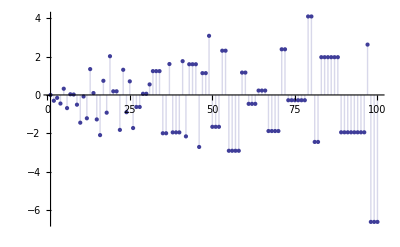

```mathematica
DiscretePlot[EL2toEL1[n,0,aa=1.1],{n,1,100}]
```

```mathematica
$RecursionLimit=10000
```

```mathematica
10000
cheb[n_,z_,b_]:=FactorialPower[z-1,0]/0! EL2[n,1,b]+Sum[ Log[b](b^a)+FactorialPower[z-1,a]/a! EL2[n,a+1,b],{a,1,Log[If[ b<2,b,2],n]}]
cheb2[n_,b_]:= EL2[n,1,b]+Sum[ Log[b](b^a)+FactorialPower[-1,a]/a! EL2[n,a+1,b],{a,1,Log[If[ b<2,b,2],n]}]
```

```mathematica
EL2a[n_, k_,b_ ]:= EL2a[n,k,b]= Sum[ EL2a[ n/j,k-1,b],{j,2,n}]-b Sum[ EL2a[ n/(j b),k-1,b],{j,1,n}]
EL2a[n_, 1,b_] :=EL2a[n,1,b]= Sum[ Log[j],{j,2,n}]-b Sum[ Log[j b],{j,1,n/b}]
cheb3[n_,b_]:= EL2a[n,1,b]+Sum[ Log[b]b^a+(-1)^a EL2a[n,a+1,b],{a,1,Log[If[ b<2,b,2],n]}]
cheb3a[n_,b_]:= Sum[ (-1)^a EL2a[n,a+1,b],{a,0,Log[If[ b<2,b,2],n]}]
cheb3b[n_,b_]:= Sum[ Log[b]b^a,{a,1,Log[If[ b<2,b,2],n]}]
cheb4[n_,b_]:= Sum[ Log[b]b^a,{a,1,Log[If[ b<2,b,2],n]}]+Sum[ (-1)^a EL2a[n,a+1,b],{a,0,Log[If[ b<2,b,2],n]}]
c2[n_] := Sum[ MangoldtLambda[j],{j,1,n}]
```

```mathematica
cheb4[100,1.1]
```

94.0453

```mathematica
cheb3b[100,1.000001]
```

99.

```mathematica
N[c2[100.]]
```

94.0453

```mathematica
EL2a[100,1,1.000001]
```

4.60471

```mathematica
EL2b[n_, k_,b_ ]:= Sum[ EL2b[ n/j,k-1,b],{j,2,n}]-b Sum[ EL2b[ n/(j b),k-1,b],{j,1,n}]
EL2b[n_, 1,b_] :=Sum[ Log[j],{j,2,n}]-b Sum[ Log[j b],{j,1,n/b}]
EL2c[n_, 1,b_] :=Sum[ Log[j],{j,2,n}]-b Sum[ Log[j],{j,1,n/b}]-b Log[b]Floor[n/b]
```

```mathematica
N[EL2b[12,3,1.0000001]]
```

2.4849

```mathematica
N[Log[4]+Log[3]]
```

2.48491

```mathematica
N[Log[3]]
```

1.09861

```mathematica
Table[ {a,(-1)^a EL2a[n,a+1,b]},{a,1,3+Log[If[ b<2,b,2],n]}]/.{n->5,b->1.02}//TableForm
```

Table::iterb: Iterator {a, 1, 3 + Log[n]/Log[If[b < 2, b, 2]]} does not have appropriate bounds.

1 | -0.149136
2 | -0.154058
3 | -0.159125
4 | -0.164342
5 | -0.169712
6 | -0.17524
7 | -0.180931
8 | -0.186788
9 | -0.192816
10 | -0.19902
11 | 13.1815
12 | -12.1015
13 | -0.138065
14 | -0.141871
15 | -0.145775
16 | -0.149778
17 | -0.153882
18 | -0.158091
19 | -0.162407
20 | -0.166832
21 | -0.171369
22 | -0.176021
23 | -0.180791
24 | -0.185681
25 | 2.50933
26 | -0.108032
27 | -0.110869
28 | -0.113776
29 | -0.116754
30 | -0.119807
31 | -0.122935
32 | -0.12614
33 | -0.129424
34 | -0.132789
35 | -0.136237
36 | -0.139769
37 | -0.143389
38 | -0.147097
39 | -0.150896
40 | -0.154789
41 | -0.158777
42 | -0.162862
43 | -0.167047
44 | -0.171335
45 | -0.175727
46 | 3.93847
47 | -0.0512308
48 | -0.0522554
49 | -0.0533005
50 | -0.0543665
51 | -0.0554539
52 | -0.0565629
53 | -0.0576942
54 | -0.0588481
55 | -0.060025
56 | -0.0612255
57 | -0.06245
58 | -0.063699
59 | -0.064973
60 | -0.0662725
61 | -0.0675979
62 | -0.0689499
63 | -0.0703289
64 | -0.0717355
65 | -0.0731702
66 | -0.0746336
67 | -0.0761263
68 | -0.0776488
69 | -0.0792018
70 | -0.0807858
71 | -0.0824015
72 | -0.0840495
73 | -0.0857305
74 | -0.0874451
75 | -0.089194
76 | -0.0909779
77 | -0.0927975
78 | -0.0946534
79 | -0.0965465
80 | -0.0984774
81 | 0.
82 | 0.
83 | 0.
84 | 0.